# Homework 2

This short notebook will provide examples of several of the basic computational tasks you will need to do in this class when solving differential equations both analytically and numerically. You should just be able to click through the notebook, but please take the time to carefully read the text and examine the code. You will be solving lots of differential equations throughout the semester, so it is worth taking the time to learn this basic functionality in Mathematica!

## Problem 2.1: Solving differential equations analytically with DSolve

```mathematica
Quit[]
```

For this example, we will use a simple linear, second-order, ordinary differential equation:
y’’(x) = -y(x)

First, we write the equation and assign a variable name to the equation (we’ll call it eq1). Note that we use a single equals sign (=) for variable assignment, but we use a double equals sign (==) when writing the actual differential equation.

```mathematica
eq1 = y''[x] == -y[x]
```

y''[x]==-y[x]

Now we can solve the equation using the DSolve function. If we don’t provide any boundary conditions, it will just give us a general solution with unspecified constants.

```mathematica
sol1 = DSolve[eq1,y[x], x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

Let’s now provide boundary conditions, one for y[x=0] and the other for y’[x=0]. We bracket these together with the original eq1. Notice that we use double equals signs when providing the boundary conditions.

```mathematica
sol2 = DSolve[{eq1, y'[0]==0, y[0]==1}, y[x], x]
```

{{y[x]→Cos[x]}}

Great! Now we have a solution! But Mathematica provides the solution as a nested list with a replacement rule (not really sure why, but that’s just the way it is). So to do something more with the solution, such as plot it, we have to use the trick shown below.

```mathematica
y=y[x]/.sol2[[1]][[1]]
```

Cos[x]

Now we can plot it.

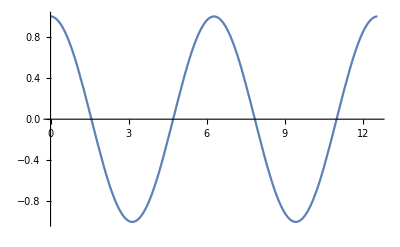

```mathematica
Plot[y,{x,0,4Pi}]
```

And we can also evaluate the solution at specific values of x:

```mathematica
y/.x->5
y/.x->2Pi
```

Cos[5]

1

## Problem 2.2: Solving differential equations numerically with NDSolve

```mathematica
Quit[]
```

Now we’ll use a nastier differential equation that can’t be solved analytically. In this case, x(t) is the function we wish to solve for, and t is the independent variable. For concreteness, we can say that t is time, although this is not in any way a physically meaningful differential equation.

x’’[t] - ( x’[t] )^2  + x[t] = 0

As before, we first write the equation and assign a variable name to the equation (we’ll call it eq1). Note the use of single and double equals signs.

```mathematica
eq1 = x''[t] - (x'[t])^2+x[t] == 0
```

x[t]-x'[t]^2+x''[t]==0

When solving analytically, we were able to come up with a general solution without specifying any boundary conditions (aka initial conditions). That is not possible when solving numerically; you must provide boundary conditions to make it work. For our boundary conditions, let’s use x’(0) = -0.5 and x(0) = 2.0. Again, we use double equals signs for the boundary condition equations. For convenience, we are assigning a variable bc to the list of boundary condition equations.

```mathematica
bc = {x'[0]==-0.5, x[0]==2.0}
```

{x'[0]==-0.5,x[0]==2.}

Now we can solve the differential equation with the given boundary conditions. The only difference from before is that we must now explicitly give the domain of the independent variable over which we are solving the equation. Let’s solve up to the first 10 seconds.

```mathematica
tStart = 0
tEnd = 10
sol1 = NDSolve[{eq1, bc}, x[t], {t,tStart,tEnd}]
```

0

10

{{x[t]→InterpolatingFunction[…][t]}}

We use another replacement rule to plot the solution.

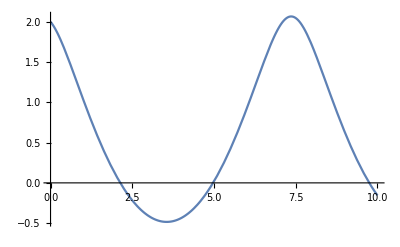

```mathematica
Plot[x[t]/.sol1,{t,tStart,tEnd}]
```

And we can also evaluate the solution at specific values of x. Notice that the last one gives you a warning because we are plugging in t = 10.1, which is outside the domain on which the equation was solved. If you really want to know the position at t=10.1 s, it would be best to go back and adjust the domain when you are using NDSolve.

```mathematica
x[t]/.sol1/.t->3.4
x[t]/.sol1/.t->10.0
x[t]/.sol1/.t->10.1
```

## Written Problems

-Graphics-

-Graphics-